## JPG-Submission

## Testing the parameters for Pr135 energy fit

### The set of parameters ℐ_1,ℐ_2,ℐ_3,θ given at j=11/2and low-lying states, must verify some validity conditions

### More precisely, these parameters (which are used at constructing the inertial functions A,v_0,u,k) must define:

provide real wobbling frequencies: for ω(θ) and its chiral partnert ω(θ+π)

provide real values for A, v_0 and u (or k, respectively)

The parameter A must also be positive

The parameter u: u>0, u<1

The potential V(q), defined from the functions A,v_0,u,k must also define a physical quantity

## Params obtained from C++ algorithm

### I_step=10 θ_step=1

```mathematica
params={91,11,61,-57};
j11=11/2;
spinValue=19/2;
```

### Formulas

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

### Jacobi Functions - Functions for the elliptic variables

```mathematica
fiVar[q_,k_]:=JacobiAmplitude[q,k^2];
```

### Potential expression

```mathematica
vRotor[I_,q_,k_,v_]:=(I(I+1)k^2+v^2)Sin[fiVar[q,k]]^2+(2I+1)v*Cos[fiVar[q,k]]*√(1-k^2 Sin[fiVar[q,k]]^2);
```

```mathematica
rotorPlot[I_,i1_,i2_,i3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,IF[i1],IF[i2],IF[i3],j,θ],v0fct[I,IF[i1],IF[i2],j,θ]],{q,-8,8},AspectRatio->0.8,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"q [rad]","V(q) [ℏ^2]"},(*PlotLegends->Placed[{"I=19/2"},{0.15,0.85}],*)FrameStyle->Directive[Black,Thick],Epilog->Inset[Style[StringTemplate["θ=(``)^o"][θ*180/π],18,Bold,Black,FontFamily->"Times New Roman"],Scaled[{0.3,0.15}]],FrameTicks->{{Automatic,None},{{-8,-4,0,4,8},None}},PlotRange->All];
```

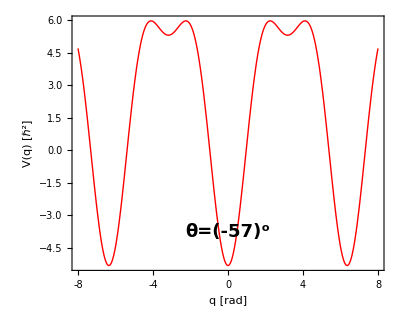

```mathematica
rotorPlot[9.5, params[[1]],params[[2]],params[[3]],5.5,params[[4]]*π/180]
```

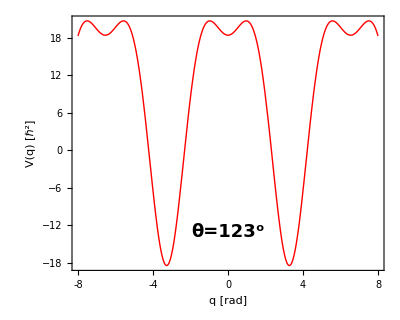

```mathematica
rotorPlot[9.5, params[[1]],params[[2]],params[[3]],5.5,(params[[4]]+180)*π/180]
```

```mathematica
Afct[9.5, IF[params[[1]]],IF[params[[2]]],5.5,params[[4]]*π/180]
```

0.0620303

```mathematica
ufct[9.5, IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],5.5,params[[4]]*π/180]
```

0.0435628

```mathematica
kfct[9.5, IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],5.5,params[[4]]*π/180]
```

0.208717

```mathematica
v0fct[9.5, IF[params[[1]]],IF[params[[2]]],5.5,params[[4]]*π/180]
```

-0.265336

## Energy Function

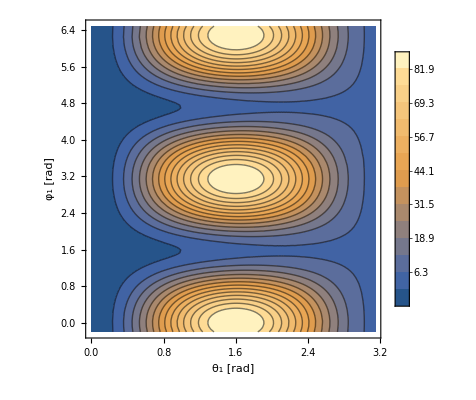

```mathematica
Hen[I_,a1_,a2_,a3_,j_,theta_,θ_,ϕ_]:=(Cos[ϕ]^2+ufct[I,a1,a2,a3,j,theta] Sin[ϕ]^2)I^2*Sin[θ]^2+2I*v0fct[I,a1,a2,j,theta]Cos[θ];
contour[I_,i1_,i2_,i3_,j_,theta_]:=ContourPlot[Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,θ,ϕ],{θ,0,π},{ϕ,-0.2,2π+0.2},PlotLegends->Automatic,Contours->14,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ_1 [rad]","φ_1 [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}];
Show[contour[9.5,params[[1]],params[[2]],params[[3]],5.5,params[[4]]]]
```

### I_step=1 θ_step=1

## c++ params 91 9 51 - 119 ENERGY RMS : 0.174715

```mathematica
paramsFit={91,9,51,-119};
```

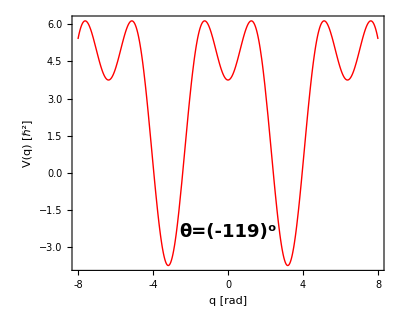

```mathematica
rotorPlot[9.5, paramsFit[[1]],paramsFit[[2]],paramsFit[[3]],5.5,paramsFit[[4]]*π/180]
```

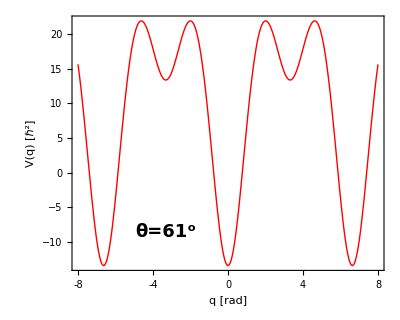

```mathematica
rotorPlot[9.5, paramsFit[[1]],paramsFit[[2]],paramsFit[[3]],5.5,(paramsFit[[4]]+180)*π/180]
```

## Construct the critical points

```mathematica
(*maximum point*)
point[X1_,Y1_,text_,x_,y_]:=Graphics[{Red,PointSize[0.021],Point[{X1,Y1}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Red,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
```

```mathematica
(*maximum point*)
pointBlue[X1_,Y1_,text_,x_,y_]:=Graphics[{Blue,PointSize[0.021],Point[{X1,Y1}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Blue,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
```

### First maximum point P1 for fixed φ_1

```mathematica
minimum[i1_,i2_,i3_,theta_,left_,right_]:=Print[NMinimize[{Hen[19/2,IF[i1],IF[i2],IF[i3],j11,theta*π/180,1.3954548323168299,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]]];
minimum[91,9,51,-119,4,6]
```

ϕ→4.71239

### First maximum point P1 for fixed θ_1

```mathematica
maximum[i1_,i2_,i3_,theta_,left_,right_]:=Print[NMaximize[{Hen[19/2,IF[i1],IF[i2],IF[i3],j11,theta*π/180,1.5887885344756139,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]]];
maximum[91,9,51,-119,4,7]
```

ϕ→6.28319

```mathematica
N[ArcCos[v0fct[9.5,IF[paramsFit[[1]]],IF[paramsFit[[2]]],5.5,paramsFit[[4]]*π/180]/(ufct[9.5,IF[paramsFit[[1]]],IF[paramsFit[[2]]],IF[paramsFit[[3]]],5.5,paramsFit[[4]]]*9.5)]]
```

1.39545

```mathematica
N[ArcCos[v0fct[9.5,IF[paramsFit[[1]]],IF[paramsFit[[2]]],5.5,paramsFit[[4]]*π/180]/9.5]]
```

1.55107

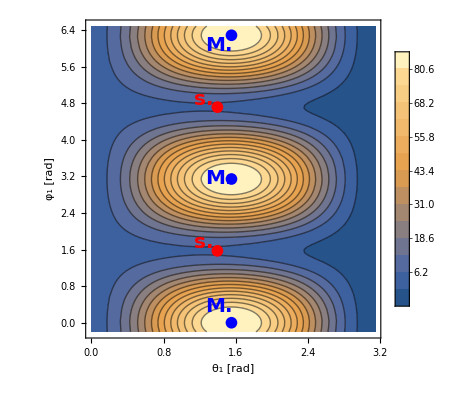

```mathematica
Show[contour[9.5,paramsFit[[1]],paramsFit[[2]],paramsFit[[3]],5.5,paramsFit[[4]]],point[1.3954548323168299,π/2,"s.",0.4,0.3],point[1.3954548323168299,4.71238898038469,"s.",0.4,0.75],pointBlue[1.5510719065697658,0,"M.",0.45,0.1],pointBlue[1.5510719065697658,3.141592653589793,"M.",0.45,0.5],pointBlue[1.5510719065697658,6.283185307179586,"M.",0.45,0.92]]
```